```mathematica
SetDirectory[NotebookDirectory[]];
EIntegrand1[x_,τ_, x0_]:= If[τ<= 10,(Sqrt[3]BesselI[0,0])/2 NIntegrate[Exp[-Sqrt[3] Abs[x-y]] UnitStep[τ - Sqrt[3] Abs[x-y]],{y,-x0, x0 },Method->"LocalAdaptive"],(Sqrt[3]BesselI[0,0])/2 NIntegrate[Exp[-Sqrt[3] Abs[x-y]] UnitStep[τ - Sqrt[3] Abs[x-y]]UnitStep[10-τ + Sqrt[3] Abs[x-y]],{y,-x0,x0 },Method->"LocalAdaptive",MaxRecursion->20]];
```

```mathematica
EIntegrand2[x_,τ_, x0_]:= If[τ<= 10,Sqrt[3]/2 NIntegrate[(Exp[-t] t BesselI[1,Sqrt[t^2-3(x-y)^2]])/Sqrt[t^2-3(x-y)^2] UnitStep[t - Sqrt[3] Abs[x-y]],{y,-x0,x0},{t,0,τ},Exclusions->t==3(x-y),Method->"LocalAdaptive"],Sqrt[3]/2 NIntegrate[(Exp[-t] t BesselI[1,Sqrt[t^2-3(x-y)^2]])/Sqrt[t^2-3(x-y)^2] UnitStep[t - Sqrt[3] Abs[x-y]],{y,-x0,x0},{t,τ-10,τ},Exclusions->t==3(x-y),Method->"LocalAdaptive",MaxRecursion->20]];
```

```mathematica
FullEInt[x_,τ_, x0_?NumericQ] := EIntegrand1[x,τ,x0] + EIntegrand2[x,τ,x0] ;
```

```mathematica
f2[x_,τ_, a1_, x0_]:= 1/2 NIntegrate[FullEInt[x, τ,x0 +a1/2 θ1 ],{θ1,-1,1}];
```

```mathematica
f3[x_,τ_, a1_, x0_]:= 1/2 NIntegrate[FullEInt[x, τ,x0 +a1/2 θ1 ]^2,{θ1,-1,1}];
```

```mathematica
f2[0,1,0.1,1/2]
```

0.661

EXPECTED VALUE OF THE SCALAR FLUX

```mathematica
teval = 1;
x0test = 0.5;
a1 = 0.25 * x0test
bound = x0test + a1 + teval/Sqrt[3];
xs = Subdivide[0,bound,20]
```

0.125

{0.,0.0601175,0.120235,0.180353,0.24047,0.300588,0.360705,0.420823,0.48094,0.541058,0.601175,0.661293,0.72141,0.781528,0.841645,0.901763,0.96188,1.022,1.08212,1.14223,1.20235}

```mathematica
PhiTableExpected=ParallelTable[{N[x],If[x< bound,f2[x,teval,a1,x0test],0]},{x,xs}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ1 near {θ1} = {0.574188}. NIntegrate obtained 0.046526 and 0.0000170947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ1 near {θ1} = {-0.710969}. NIntegrate obtained 0.182709 and 0.0000151917 for the integral and error estimates.

```mathematica
PhiTableExpected[[All, 2]]^2;
```

```mathematica
PhiTableVar=ParallelTable[{N[x],If[x< bound,f3[x,teval,a1,x0test],0]},{x,xs}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ1 near {θ1} = {0.574188}. NIntegrate obtained 0.00387041 and 1.60246×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ1 near {θ1} = {-0.710969}. NIntegrate obtained 0.0197275 and 1.25249×10^-6 for the integral and error estimates.

```mathematica
PhiTableVar[[All,2]]=PhiTableVar[[All,2]] -PhiTableExpected[[All, 2]]^2
```

{0.000778361,0.000623556,0.000362273,0.000422306,0.000531375,0.000660857,0.00081329,0.00099137,0.00116521,0.00111465,0.000923057,0.000754683,0.000610953,0.000489227,0.00151815,0.00139403,1.38519×10^-6,3.37108×10^-7,1.47034×10^-8,0.,0}

```mathematica
PhiTableExpected
```

{{0.,0.660572},{0.0601175,0.654764},{0.120235,0.634469},{0.180353,0.602708},{0.24047,0.566407},{0.300588,0.525811},{0.360705,0.480661},{0.420823,0.430697},{0.48094,0.375986},{0.541058,0.319723},{0.601175,0.266611},{0.661293,0.218439},{0.72141,0.174986},{0.781528,0.135991},{0.841645,0.0913543},{0.901763,0.023263},{0.96188,0.00204304},{1.022,0.00060792},{1.08212,0.0000711878},{1.14223,0.},{1.20235,0}}

```mathematica
PhiTableVar
```

{{0.,0.000778361},{0.0601175,0.000623556},{0.120235,0.000362273},{0.180353,0.000422306},{0.24047,0.000531375},{0.300588,0.000660857},{0.360705,0.00081329},{0.420823,0.00099137},{0.48094,0.00116521},{0.541058,0.00111465},{0.601175,0.000923057},{0.661293,0.000754683},{0.72141,0.000610953},{0.781528,0.000489227},{0.841645,0.00151815},{0.901763,0.00139403},{0.96188,1.38519×10^-6},{1.022,3.37108×10^-7},{1.08212,1.47034×10^-8},{1.14223,0.},{1.20235,0}}

```mathematica
(*PhiTableSTD = Sqrt[PhiTableVar[[All,2]]];*)
```

{0.661161,0.66103,0.660521,0.659381,0.657615,0.65524,0.652271,0.648724,0.644613,0.639952,0.634755,0.629034,0.622826,0.616394,0.609806,0.603058,0.596151,0.589081,0.581846,0.574445,0.566876,0.559137,0.551226,0.54314,0.534879,0.526439,0.51782,0.509019,0.500034,0.490864,0.481506,0.47196,0.462222,0.452292,0.442167,0.431847,0.421328,0.410612,0.399718,0.38868,0.377533,0.366313,0.355057,0.343803,0.332591,0.321462,0.310458,0.299624,0.288992,0.278563,0.268337,0.25831,0.248481,0.238848,0.229408,0.22016,0.211102,0.20223,0.193545,0.185043,0.176723,0.168582,0.160619,0.152832,0.145219,0.137778,0.130507,0.123405,0.11647,0.109292,0.0993164,0.0892513,0.0789871,0.0683142,0.0568983,0.0439909,0.0274119,0.0037214,0.00322799,0.00277352,0.00235779,0.00198048,0.00164104,0.00133869,0.00107236,0.00084064,0.00064192,0.000474469,0.000336443,0.000225867,0.00014061,0.0000783433,0.0000364848,0.000012085,1.5944×10^-6,0.,0.,0.,0.,0.,0}

```mathematica
PhiTableNormal=ParallelTable[{N[x],If[x< bound,f2[x,teval,0,x0test],0]},{x,xs}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

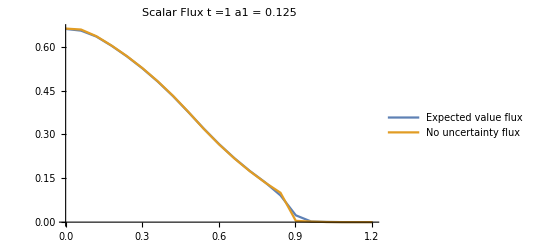

```mathematica
plot = ListPlot[{PhiTableExpected, PhiTableNormal}, Joined->True,PlotLegends->{"Expected value flux", "No uncertainty flux", "Expected value energy density", "No uncertainty Energy Density"}, PlotLabel->"Scalar Flux t =1 a1 = 0.125", PlotRange->All    ]
```

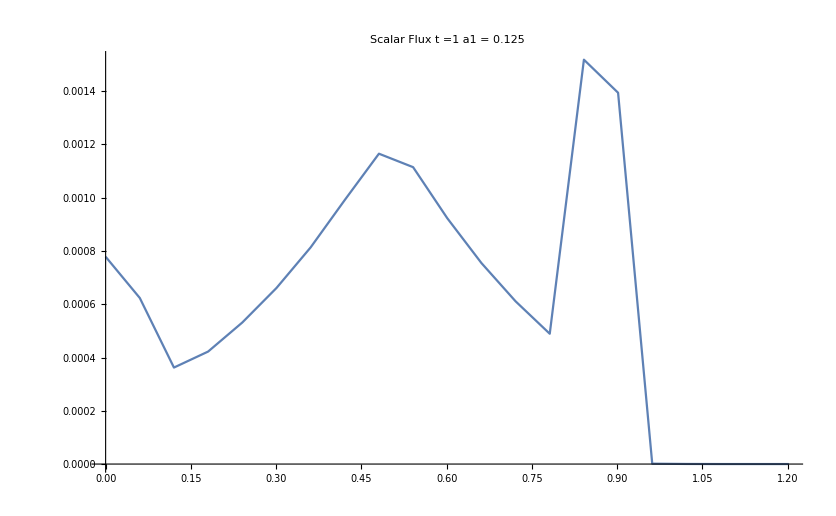

```mathematica
plot2 = ListPlot[{PhiTableVar }, Joined->True, PlotLabel->"Scalar Flux t =1 a1 = 0.125", PlotRange->All    ]
```

```mathematica
Export["SuExp_t=1_a1=0.125.pdf",plot]
```

SuExp_t=1_a1=0.125.pdf

```mathematica
PhiTableVar[[1]] 
Sqrt[PhiTableVar[[All,2]]]
```

{0.,0.000778361}

{0.0278991,0.0249711,0.0190335,0.0205501,0.0230516,0.0257071,0.0285182,0.031486,0.0341352,0.0333864,0.0303819,0.0274715,0.0247175,0.0221185,0.0389634,0.0373368,0.00117694,0.00058061,0.000121257,0.,0}

```mathematica
PhiTableSTDp = PhiTableVar *0;
PhiTableSTDm = PhiTableVar *0;
PhiTableSTDp[[All,1]] = PhiTableVar[[All,1]];
PhiTableSTDm[[All,1]] = PhiTableVar[[All,1]];
PhiTableSTDp[[All,2]] = PhiTableExpected[[All,2]] + Sqrt[PhiTableVar[[All,2]]];
PhiTableSTDm[[All,2]] = PhiTableExpected[[All,2]] - Sqrt[PhiTableVar[[All,2]]];
```

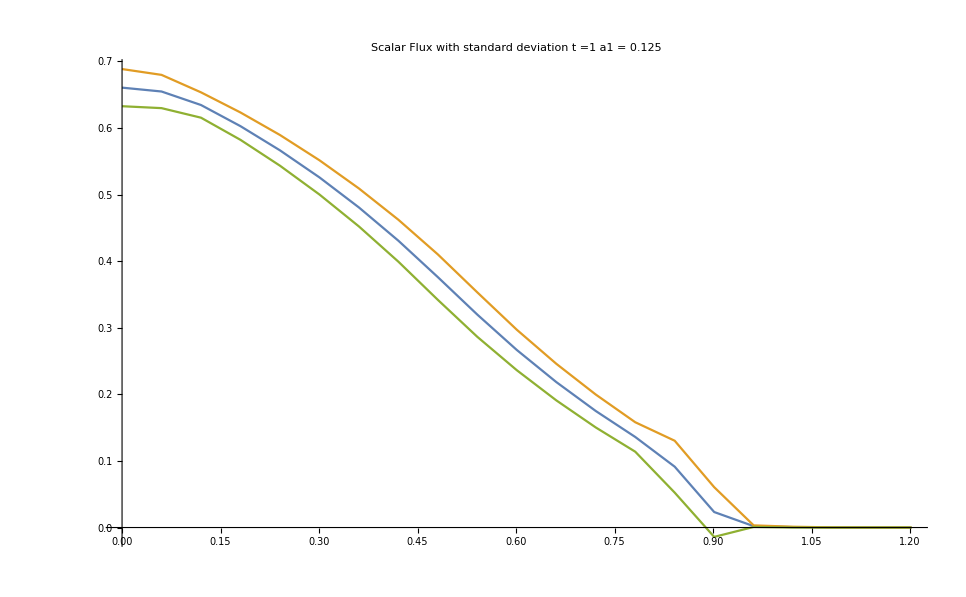

```mathematica
plot3 = ListPlot[{PhiTableExpected, PhiTableSTDp, PhiTableSTDm}, Joined->True, PlotLabel->"Scalar Flux with standard deviation t =1 a1 = 0.125", PlotRange->All    ]
```

```mathematica
Integrate[1/(x-1)^4 Exp[-x^2/2],{x,-∞,∞}]
```

Integrate::idiv: Integral of (ⅇ^(-x^2/2))/(-1+x)^4 does not converge on {-∞,∞}.

∫_(-∞)^∞ (ⅇ^(-x^2/2))/(-1+x)^4 ⅆx